```mathematica
vt=Solve[(((c^2 ut'^2-n^2(ux'^2+uy'^2))/ut^2)/.{ut'->γ(c ut - β ux), ux'-> γ(ux - β c ut), uy'->uy}/. {ux -> ut*v[θ]*Cos[θ], uy-> ut*v[θ]*Sin[θ]}//FullSimplify)==0, v[θ]]
```

{{v[θ]→(-2 c^3 β γ^2 Cos[θ]+2 c n^2 β γ^2 Cos[θ]-√(4 c^4 n^2 γ^4 Cos[θ]^2-8 c^4 n^2 β^2 γ^4 Cos[θ]^2+4 c^4 n^2 β^4 γ^4 Cos[θ]^2+4 c^4 n^2 γ^2 Sin[θ]^2-4 c^2 n^4 β^2 γ^2 Sin[θ]^2))/(2 (n^2 γ^2 Cos[θ]^2-c^2 β^2 γ^2 Cos[θ]^2+n^2 Sin[θ]^2))},{v[θ]→(-2 c^3 β γ^2 Cos[θ]+2 c n^2 β γ^2 Cos[θ]+√(4 c^4 n^2 γ^4 Cos[θ]^2-8 c^4 n^2 β^2 γ^4 Cos[θ]^2+4 c^4 n^2 β^4 γ^4 Cos[θ]^2+4 c^4 n^2 γ^2 Sin[θ]^2-4 c^2 n^4 β^2 γ^2 Sin[θ]^2))/(2 (n^2 γ^2 Cos[θ]^2-c^2 β^2 γ^2 Cos[θ]^2+n^2 Sin[θ]^2))}}

```mathematica
((c^2 ut'^2-n^2(ux'^2+uy'^2))/ut^2)/.{ut'->γ(c ut - β ux), ux'-> γ(ux - β c ut), uy'->uy}//FullSimplify
```

(c^2 (c ut-ux β)^2 γ^2-n^2 (uy^2+(ux-c ut β)^2 γ^2))/ut^2

```mathematica
vt[[2]]
```

{v[θ]→(-2 c β γ^2 Cos[θ]+2 c n^2 β γ^2 Cos[θ]+√((-2 c β γ^2 Cos[θ]+2 c n^2 β γ^2 Cos[θ])^2-4 (c^2 γ^2-c^2 n^2 β^2 γ^2) (-n^2 γ^2 Cos[θ]^2+β^2 γ^2 Cos[θ]^2-n^2 Sin[θ]^2)))/(2 (n^2 γ^2 Cos[θ]^2-β^2 γ^2 Cos[θ]^2+n^2 Sin[θ]^2))}

```mathematica
v[θ]/.vt[[2]]/.c->1//FullSimplify
```

((-1+n^2) β γ^2 Cos[θ]+√(n^2 γ^2 ((-1+β^2)^2 γ^2 Cos[θ]^2+(1-n^2 β^2) Sin[θ]^2)))/((n-β) (n+β) γ^2 Cos[θ]^2+n^2 Sin[θ]^2)

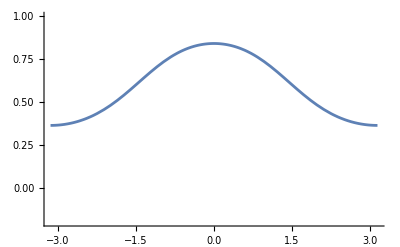

(1.19048 Cos[θ]-√(9. Cos[θ]^2+6.85714 Sin[θ]^2))/(2 (2.4881 Cos[θ]^2+2.25 Sin[θ]^2))

```mathematica
Show[
Plot[v[θ]/.vt[[1]]/. (γ->1/Sqrt[1-β^2])/.{c->1, n->1.5, β->0.4}, {θ, -π, π}],
Plot[v[θ]/.vt[[2]]/.γ->1/Sqrt[1-β^2]/.{c->1, n->1.5, β->0.4}, {θ, -π, π}],
PlotRange->{{-π, π}, {-0.2, 1}}
]
```

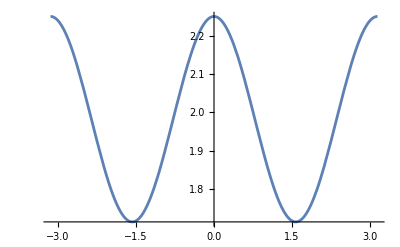

```mathematica
Plot[(n^2 γ^2 ((-1+β^2)^2 γ^2 Cos[θ]^2+(1-n^2 β^2) Sin[θ]^2))/. (γ->1/Sqrt[1-β^2])/.{c->1, n->1.5, β->0.4}, {θ, -π, π}]
```